General::ovfl: Overflow occurred in computation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

{{p1[t]→InterpolatingFunction[…][t],p2[t]→InterpolatingFunction[…][t],p3[t]→InterpolatingFunction[…][t],p4[t]→InterpolatingFunction[…][t]}}

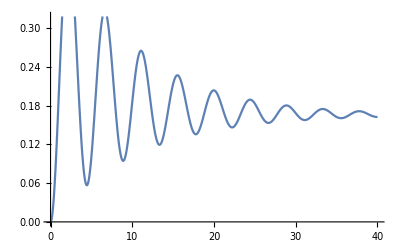

```mathematica
Clear["Global`*"] (* This command clears everything *)

(*Define pauli matricies, variables, and P matricies*)
Δ = 1; ν = 0; ϵ = 1; T= 298; k = 1.382*^-23; α = 1/(12*Pi);
n = 1/(Exp[ϵ/(k*T)]-1);
η = Sqrt[ν^2+Δ^2];
Γ0 = 4*Pi*α*k*T;
Γn = 2*Pi*α*η;
sz = {{ϵ/η,-Δ/η},{-Δ/η,-ϵ/η}};
sx = {{Δ/η,ϵ/η},{ϵ/η,-Δ/η}};
P0 = {{ϵ/η,0},{0,-ϵ/η}};
Pn = {{0,0},{Δ/η,0}};
Pnd = ConjugateTranspose[Pn];

(*System Hamiltonian*)
Hs = ν/2*sz + Δ/2*sx;

(*density matrix to solve*)
p[t_] := {{p1[t],p2[t]},{p3[t],p4[t]}}

sol = NDSolve[{p'[t] == -ⅈ*(Hs.p[t]-p[t].Hs)+Γ0*(P0.p[t].P0-1/2*(P0.P0.p[t]+p[t].P0.P0))+Γn*(1+n)*(Pn.p[t].Pnd-1/2*(Pnd.Pn.p[t]+p[t].Pnd.Pn))+Γn*n*(Pnd.p[t].Pn-1/2*(Pn.Pnd.p[t]+p[t].Pn.Pnd)),p[0] == {{0,0},{0,1}}},{p1[t],p2[t],p3[t],p4[t]},{t,0,40}]

Plot[p1[t]/.sol,{t,0,40}]
```